```mathematica
ClearAll["Global`*"]
```

```mathematica
S1[k_,V_,K_]:=S/.Simplify[Solve[k(2-S)==(V*S)/(K+S),S]][[1]]
S2[k_,V_,K_]:=S/.Simplify[Solve[2*k(2-S)==(V*S)/(K+S),S]][[1]]
S3[k_,V_,K_]:=S/.Simplify[Solve[k(2-S)==(2*V*S)/(K+S),S]][[1]]
```

```mathematica
Jac[k_,V_,K_]:=Simplify[{{D[S1[k,V,K],k],D[S1[k,V,K],V],D[S1[k,V,K],K]},{D[S2[k,V,K],k],D[S2[k,V,K],V],D[S2[k,V,K],K]},{D[S3[k,V,K],k],D[S3[k,V,K],V],D[S3[k,V,K],K]}}]
```

```mathematica
Jac[k,V,K]//MatrixForm
```

((V (2 k-k K-V+√(8 k^2 K+(k (-2+K)+V)^2)))/(2 k^2 √(8 k^2 K+(k (-2+K)+V)^2)) | (-1+(k (-2+K)+V)/(√(8 k^2 K+(k (-2+K)+V)^2)))/(2 k) | 1/2 (-1+(k (2+K)+V)/(√(8 k^2 K+(k (-2+K)+V)^2)))
(V (4 k-2 k K-V+√(32 k^2 K+(2 k (-2+K)+V)^2)))/(4 k^2 √(32 k^2 K+(2 k (-2+K)+V)^2)) | (-1+(2 k (-2+K)+V)/(√(32 k^2 K+(2 k (-2+K)+V)^2)))/(4 k) | 1/2 (-1+(2 k (2+K)+V)/(√(32 k^2 K+(2 k (-2+K)+V)^2)))
(V (2 k-k K-2 V+√(8 k^2 K+(k (-2+K)+2 V)^2)))/(k^2 √(8 k^2 K+(k (-2+K)+2 V)^2)) | (-2+(2 (k (-2+K)+2 V))/(√(8 k^2 K+(k (-2+K)+2 V)^2)))/(2 k) | 1/2 (-1+(k (2+K)+2 V)/(√(8 k^2 K+(k (-2+K)+2 V)^2))))

```mathematica
SingularValueDecomposition[N[Jac[k,V,K]/.{k->1,V->1,K->1}]]
```

{{{-0.560697,0.513461,0.649597},{-0.326259,0.584053,-0.743261},{-0.761035,-0.628681,-0.159955}},{{1.31355,0.,0.},{0.,0.0414212,0.},{0.,0.,0.}},{{-0.672578,0.218262,-0.707107},{0.672578,-0.218262,-0.707107},{-0.308669,-0.95117,-2.58392×10^-17}}}

```mathematica
Simplify[D[(2 k-k K-V+√(8 k^2 K+(k (-2+K)+V)^2))/(2 k),K]]
```

1/2 (-1+(k (2+K)+V)/(√(8 k^2 K+(k (-2+K)+V)^2)))

```mathematica
J[k1_,k2_]:=(k1*k2)/(k1+k2);
```

```mathematica
dJdk1[k1_,k2_]:=Simplify[D[J[k1,k2],k1]]
dJdk1[k1,k2]
```

k2^2/(k1+k2)^2

```mathematica
dJdk1[k1_,k2_]:=Simplify[D[J[k1,k2],k1]]
dJdk2[k1_,k2_]:=Simplify[D[J[k1,k2],k2]]
```

```mathematica
dJdk1[k1,r*k2]
Jac[k1_,k2_,r_]:={{dJdk1[k1,k2],dJdk2[k1,k2]},{r* dJdk1[r*k1,k2],dJdk2[r*k1,k2]},{dJdk1[k1,r*k2],r*dJdk2[k1,r*k2]}}
Jac[k1,k2,r]
```

(k2^2 r^2)/(k1+k2 r)^2

General::ivar: k1\ r is not a valid variable.

General::ivar: k2\ r is not a valid variable.

{{k2^2/(k1+k2)^2,k1^2/(k1+k2)^2},{r ∂_(k1 r) (k1 k2 r)/(k2+k1 r),(k1^2 r^2)/(k2+k1 r)^2},{(k2^2 r^2)/(k1+k2 r)^2,r ∂_(k2 r) (k1 k2 r)/(k1+k2 r)}}

```mathematica
(*Jac[k1_,k2_,r_]:={{k2^2/(k1+k2)^2,k1^2/(k1+k2)^2},{(r*k2^2)/(r*k1+k2)^2,k1^2/(r*k1+k2)^2},{k2^2/(k1+r*k2)^2,(r*k1^2)/(k1+r*k2)^2}};*)
```

```mathematica
dJdk1[k1,k2]
Jac[k1,k2,r]
```

k2^2/(k1+k2)^2

General::ivar: k1\ r is not a valid variable.

General::ivar: k2\ r is not a valid variable.

{{k2^2/(k1+k2)^2,k1^2/(k1+k2)^2},{r ∂_(k1 r) (k1 k2 r)/(k2+k1 r),(k1^2 r^2)/(k2+k1 r)^2},{(k2^2 r^2)/(k1+k2 r)^2,r ∂_(k2 r) (k1 k2 r)/(k1+k2 r)}}

```mathematica
Jac2[ρ_,r_]:=Simplify[Jac[k1,k2,r]/.{k2->ρ*k1}]
Jac2[ρ,r]
```

General::ivar: k1\ r is not a valid variable.

General::ivar: k2\ r is not a valid variable.

General::ivar: k1\ r is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

{{ρ^2/(1+ρ)^2,1/(1+ρ)^2},{r ∂_(k1 r) (k1 r ρ)/(r+ρ),r^2/(r+ρ)^2},{(r^2 ρ^2)/(1+r ρ)^2,r ∂_(k1 r ρ) (k1 r ρ)/(1+r ρ)}}

```mathematica
SingularValueDecomposition[Jac2[ρ,r]]
```

SingularValueDecomposition[Jac2[ρ,r]]

```mathematica
Assuming[ρ>0&&r>0,SingularValueDecomposition[Jac2[ρ,r]]]
```

$Aborted

```mathematica
FullSimplify[SingularValueDecomposition[{{dJdk1[k1,k2],dJdk2[k1,k2]}}], k1>0&&k2>0]
```

{{{1}},{{(√(k1^4+k2^4))/(k1+k2)^2,0}},{{k2^2/(√(k1^4+k2^4)),-k1^2/(√(k1^4+k2^4))},{k1^2/(√(k1^4+k2^4)),1/(√(1+k1^4/k2^4))}}}

```mathematica
Jac[ρ_,r_]:={{(ρ/(1+ρ))^2,(1/(1+ρ))^2},{r(ρ/(r+ρ))^2,(1/(r+ρ))^2},{(ρ/(1+r*ρ))^2,r(1/(1+r*ρ))^2}};
```

```mathematica
Simplify[SingularValueDecomposition[Jac[ρ,r]/.ρ->1], r>1]
```

{{{0,(1+r)/(√(9+2 r+r^2)),-(2 √2)/(√(8+(1+r)^2))},{-1/(√2),2/(√(9+2 r+r^2)),1/(√(2+16/(1+r)^2))},{1/(√2),2/(√(9+2 r+r^2)),1/(√(2+16/(1+r)^2))}},{{(-1+r)/(1+r)^2,0},{0,(√(9+2 r+r^2))/(√2 (2+2 r))},{0,0}},{{-1/(√2),1/(√2)},{1/(√2),1/(√2)}}}

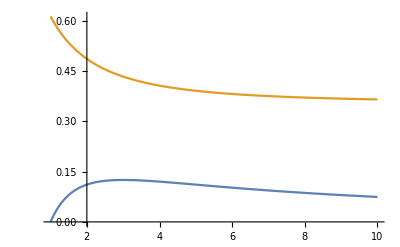

```mathematica
Plot[{(-1+r)/(1+r)^2,(√(9+2 r+r^2))/(√2 (2+2 r))},{r,1,10}]
```

```mathematica
FullSimplify[Transpose[Jac[ρ,r]].Jac[ρ,r]]//MatrixForm
```

(ρ^4 (1/(1+ρ)^4+r^2/(r+ρ)^4+1/(1+r ρ)^4) | ρ^2 (1/(1+ρ)^4+r (1/(r+ρ)^4+1/(1+r ρ)^4))
ρ^2 (1/(1+ρ)^4+r (1/(r+ρ)^4+1/(1+r ρ)^4)) | 1/(1+ρ)^4+1/(r+ρ)^4+r^2/(1+r ρ)^4)

```mathematica
Factor[(r+ρ)^4(1+r ρ)^4+r^2(1+ρ)^4(1+r ρ)^4+(1+ρ)^4(r+ρ)^4]
```

r^2+2 r^4+4 r^2 ρ+12 r^3 ρ+4 r^4 ρ+4 r^5 ρ+18 r^2 ρ^2+32 r^3 ρ^2+28 r^4 ρ^2+6 r^6 ρ^2+8 r ρ^3+28 r^2 ρ^3+72 r^3 ρ^3+28 r^4 ρ^3+28 r^5 ρ^3+4 r^7 ρ^3+2 ρ^4+16 r ρ^4+53 r^2 ρ^4+32 r^3 ρ^4+73 r^4 ρ^4+16 r^5 ρ^4+17 r^6 ρ^4+r^8 ρ^4+4 ρ^5+28 r ρ^5+24 r^2 ρ^5+32 r^3 ρ^5+24 r^4 ρ^5+48 r^5 ρ^5+4 r^6 ρ^5+4 r^7 ρ^5+6 ρ^6+16 r ρ^6+12 r^2 ρ^6+22 r^4 ρ^6+16 r^5 ρ^6+12 r^6 ρ^6+4 ρ^7+4 r ρ^7+4 r^3 ρ^7+8 r^5 ρ^7+4 r^6 ρ^7+ρ^8+r^4 ρ^8+r^6 ρ^8

```mathematica
((r+ρ)^4(1+r ρ)^4+(1+ρ)^4(1+r ρ)^4+r^2(1+ρ)^4(r+ρ)^4)
```

```mathematica
J1={1,2,3};J2={1,1,1};
N[SingularValueDecomposition[Transpose[{J1,J2}]]]
```

{{{0.32311,0.853776,0.408248},{0.547507,0.18322,-0.816497},{0.771904,-0.487337,0.408248}},{{4.07914,0.},{0.,0.600491},{0.,0.}},{{0.915348,-0.402663},{0.402663,0.915348}}}

```mathematica
FindMinimum[Norm[J1*Cos[θ]+J2*Sin[θ]],0]
```

FindMinimum::fdssnv: Search specification 0 without variables should be a list with 1 to 4 elements.

```mathematica
θmin=θ/.FindMinimum[Norm[J1 Cos[θ]+J2 Sin[θ]],{θ,0}][[2]]
```

-1.15637

```mathematica
{Cos[θ],Sin[θ]}/.{θ->θmin}
```

{0.402663,-0.915348}

```mathematica
Transpose[Jac[ρ,r]]
```

{{ρ^2/(1+ρ)^2,(r ρ^2)/(r+ρ)^2,ρ^2/(1+r ρ)^2},{1/(1+ρ)^2,1/(r+ρ)^2,r/(1+r ρ)^2}}

```mathematica
J1[ρ_,r_]:={ρ^2/(1+ρ)^2,(r ρ^2)/(r+ρ)^2,ρ^2/(1+r ρ)^2};J2[ρ_,r_]:={1/(1+ρ)^2,1/(r+ρ)^2,r/(1+r ρ)^2};
```

```mathematica
FindMinimum[Norm[J1[ρ,r]* Cos[θ]+J2[ρ,r]*Sin[θ]],{θ,1}]
```

FindMinimum::nrnum: The function value √Abs[0.841471/Plus[« 2 »]^2 + 0.540302\ ρ^2/Plus[« 2 »]^2]^2 + Abs[0.841471/Plus[« 2 »]^2 + 0.540302\ r\ ρ^2/Plus[« 2 »]^2]^2 + Abs[0.841471\ r/Plus[« 2 »]^2 + 0.540302\ ρ^2/Plus[« 2 »]^2]^2 is not a real number at {θ} = {1.}.

FindMinimum[Norm[J1[ρ,r] Cos[θ]+J2[ρ,r] Sin[θ]],{θ,1}]

```mathematica
Assert[{ρ>0,r>1}]
```

Assert[{ρ>0,r>1}]

```mathematica
Simplify[Norm[J1[ρ,r]* Cos[θ]+J2[ρ,r]*Sin[θ]]^2, ρ>0&&r>1&&θ>0&&θ<π]
```

((ρ^2 Cos[θ]+Sin[θ])^2)/(1+ρ)^4+((r ρ^2 Cos[θ]+Sin[θ])^2)/(r+ρ)^4+((ρ^2 Cos[θ]+r Sin[θ])^2)/(1+r ρ)^4

```mathematica
J1[ρ,r]//MatrixForm
J2[ρ,r]//MatrixForm
```

(ρ^2/(1+ρ)^2
(r ρ^2)/(r+ρ)^2
ρ^2/(1+r ρ)^2)

(1/(1+ρ)^2
1/(r+ρ)^2
r/(1+r ρ)^2)

```mathematica
J1[ρ,r]
```

{ρ^2/(1+ρ)^2,(r ρ^2)/(r+ρ)^2,ρ^2/(1+r ρ)^2}

```mathematica
N[Simplify[D[(2*k1+2*k2)/(k1+2*k2),k1]]/.{k1->1,k2->2}]
```

0.16

```mathematica
Simplify[(2*X1-2*S2)/(S2-X2)/.S2->(2*k1*X1+k2*X2)/(2*k1+k2)]
```

k2/k1

```mathematica
S[k1_,k2_]:=(k1*X1+k2*X2)/(k1+k2)/.{X1->1,X2->0};
J[k1_,k2_]:=(k1*k2)/(k1+k2);
Jp[k1_,k2_]:=(5*k1*k2)/(5*k1+k2);
Jac[k1_,k2_]:=Simplify[{{D[S[k1,k2],k1],D[S[k1,k2],k2]},{D[J[k1,k2],k1],D[J[k1,k2],k2]}}];
Jacp[k1_,k2_]:=Simplify[{{D[Jp[k1,k2],k1],D[Jp[k1,k2],k2]},{D[J[k1,k2],k1],D[J[k1,k2],k2]}}];
```

{{{-0.841047,0.540962},{-0.540962,-0.841047}},{{0.761609,0.},{0.,0.238188}},{{-0.766419,-0.64234},{-0.64234,0.766419}}}

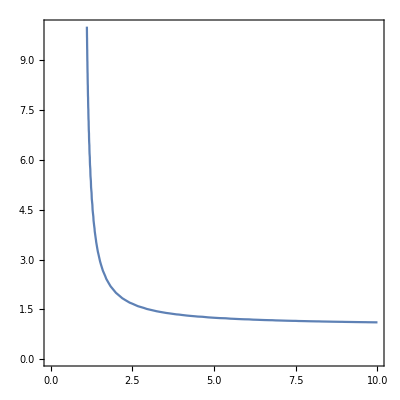

```mathematica
SingularValueDecomposition[N[Jacp[k1,k2]/.{k1->1,k2->2}]]
```